```mathematica
streak[x_, pAgain_] := If[x==-1,RandomChoice[{pAgain, 1-pAgain}-> {-1, 1}], RandomChoice[{1-pAgain, pAgain}-> {-1, 1}]]
ht[dep_, n_]:= NestList[streak[#, dep]&, -1, n]
randWalkDep[dep_, n_]:= Accumulate[NestList[streak[#, dep]&, -1, n]]
```

```mathematica
medioc =
```

```mathematica
n = 2500;
medioc =  randWalkDep[0.5, 2500];
extrem = randWalkDep[0.525, 2500];
```

```mathematica
Manipulate[
GraphicsColumn[{ 
Tooltip[ListLinePlot[Differences[medioc, d, differenceWindow], PlotRange-> {{0, n},{plotrange, -plotrange}}], "Independent Differences"],
Tooltip[ListLinePlot[Differences[extrem, d, differenceWindow], PlotRange-> {{0, n},{plotrange, -plotrange}}], "Dependent Differences"]}],
 {{d, 1, "nth derivative"}, 1, 10, 1},
{{differenceWindow, 40}, 1, 50, 1},
{{plotrange, 20}, 2, 1000,2 },
 SynchronousUpdating->False]
```

```mathematica
n = 1000;
```

```mathematica
medioc =  randWalkDep[0.5, n];
extrem = randWalkDep[0.525, n];
```

{{1,1},{-1,-1},{-1,1}}

{{159,173},{181,160},{246,247}}

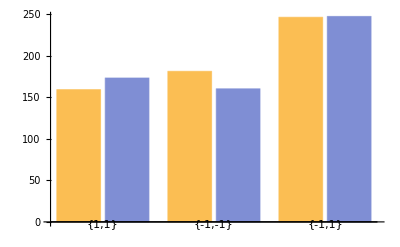

```mathematica
raw = ht[0.5, n];
rawDep = ht[0.48, n];
options = {1, -1};
combs = {{1, 1}, {-1, -1}, {-1, 1}}
counts= SequenceCount[raw,#]&/@combs;
countsDep = SequenceCount[rawDep,#]&/@combs;
bars =MapThread[{#1, #2}&, {counts, countsDep}]
BarChart[Labeled@@@Transpose[{bars, combs}]]
```

```mathematica
bars
```

{{172,165},{256,269},{256,269},{158,149}}

```mathematica
Tally[raw]
```

{{-1,511},{1,490}}

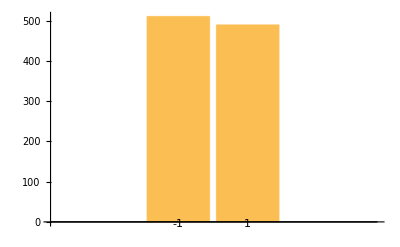

```mathematica
BarChart[Labeled@@@Reverse[{{-1,511},{1,490}},2]]
```

```mathematica
f@@@{{a, b, c}, {1, 2, 3}}
```

{f[a,b,c],f[1,2,3]}